Wigner in Fock basis. For nm the Wigner is denoted by W[n,m]

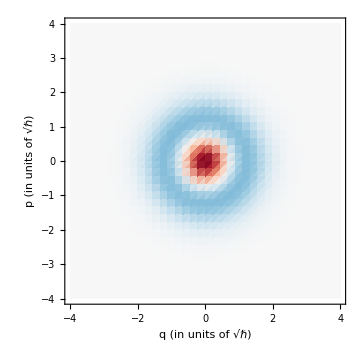

```mathematica
ℏ=1;
(* Wigner of nm. Ref: StackExchange answer to "What is the Winger of nm?" by Cosmas Zachos. *)
W[m_,n_,q_,p_]:=lim_(x->q) ((-1)^m/π √(((Min[m,n])!)/((Max[m,n])!))ⅇ^(-(q^2+p^2))(√2(-x+ⅈ p))^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],2(q^2+p^2)]);

(* Options for the density plot *)
cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
limits=4;
range=18;
n=1;
m=1;
(* Construct matrix to plot *)
mat=Table[Re[Chop[W[n,m,(q-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{q,1,2 range +1}];
(* Normalize the mat *)
mat=mat/((*Abs[ Total[mat,2]](limits/range)^2*)1);
(* Plot *)
ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{"q (in units of √ℏ)","p (in units of √ℏ)"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium]
```

```mathematica
(* OUTPUT STATE after for ideal k photon subtraction for various inputs *)
(* Plus state input to the beamsplitter *)
WkTilde[1][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/N⌉)^K ∑_(m=⌈k/N⌉)^K (1/2^K √(Binomial[K,n]Binomial[K,m])Binomial[n N, k]Binomial[m N, k] t^(n N+ m N - 2k)W[n N-k,m N-k,q,p]);

(* Minus state input *)
WkTilde[2][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/N⌉)^K ∑_(m=⌈k/N⌉)^K (1/2^K √(Binomial[K,n]Binomial[K,m])Binomial[n N, k]Binomial[m N, k] t^(n N+ m N - 2k)(-1)^(n+m)W[n N-k,m N-k,q,p]);

(* Zero state input *)
WkTilde[3][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/(2N)⌉)^⌊K/2⌋ ∑_(m=⌈k/(2N)⌉)^⌊K/2⌋ (1/2^(K-1)√(Binomial[K,2n]Binomial[K,2m])Binomial[2n N, k]Binomial[2m N, k]lim_(tL->t) (tL^(2n N+ 2m N - 2k)(1-tL^2)^k)W[2n N-k,2m N-k,q,p]);

(* One state input *)
WkTilde[4][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈(k/N-1)/2⌉)^⌊(K-1)/2⌋ ∑_(m=⌈(k/N-1)/2⌉)^⌊(K-1)/2⌋ (1/2^(K-1)√(Binomial[K,(2n+1)]Binomial[K,(2m+1)])Binomial[(2n+1) N, k]Binomial[(2m+1) N, k]lim_(tL->t) (tL^((2n+1) N+ (2m+1) N - 2k)(1-tL^2)^k)W[(2n +1)N-k,(2m+1) N-k,q,p]);

(* Normalized states *)
Wk[j_,N_,K_,k_,q_,p_,t_]:=(WkTilde[j][N,K,k,q,p,t])/(∫_(-∞)^∞ (∫_(-∞)^∞ WkTilde[j][N,K,k,q1,p1,t]ⅆp1)ⅆq1);

(* Ideal binomial codewords (no beamsplitting or detections involved) *)
W0[N_,K_,q_,p_]:=∑_(n=0)^⌊K/2⌋ ∑_(m=0)^⌊K/2⌋ (1/2^(K-1)√(Binomial[K,2n]Binomial[K,2m])W[2n N,2m N,q,p]);
W1[N_,K_,q_,p_]:=∑_(n=0)^⌊(K-1)/2⌋ ∑_(m=0)^⌊(K-1)/2⌋ (1/2^(K-1)√(Binomial[K,(2n+1)]Binomial[K,(2m+1)])W[(2n +1)N,(2m+1) N,q,p]);

(* Fidelity between normalized k photon subtracted and ZPS states for j^th-type input state as defined above as WkTilde[j][vars] *)
fidelity[j_,t_,k_]:=2π(∫_(-∞)^∞ (∫_(-∞)^∞ Wk[j,N,K,0,q,p,t]Wk[j,N,K,k,q,p,t]ⅆp)ⅆq );
```

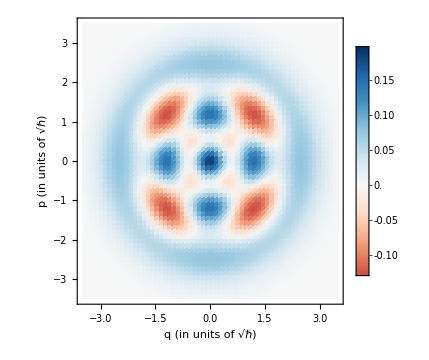

```mathematica
(* Normalized OUTPUT STATE after inefficient no-click event *)
WoutTilde[N_,K_,q_,p_,t_,η_]:=∑_(k=0)^(K N) (WkTilde[3][N,K,k,q,p,t]lim_(ηL->η) ((1-ηL)^k));
pr[N_,K_,q_,p_,t_,η_]:=∫_(-∞)^∞ (∫_(-∞)^∞ WoutTilde[N,K,q,p,t,η]ⅆp)ⅆq; (* probability of no-click *)
Wout[N_,K_,q_,p_,t_,η_]:= WoutTilde[N,K,q,p,t,η]/pr[N,K,q,p,t,η];

(* Options for the density plot *)
cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
limits=3.5;
range=30;
Num=2;
K=3;
η=0;
t=√(.98);
(* Construct matrix to plot *)
mat=Table[Re[Chop[WoutTilde[Num,K,(q-1)(limits/range)-limits,(p-1)(limits/range)-limits,t,η]]],{p,1,2 range +1},{q,1,2 range +1}];
(* Normalize the mat *)
mat=mat/(Abs[ Total[mat,2]](limits/range)^2);
(* Plot *)
ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{"q (in units of √ℏ)","p (in units of √ℏ)"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,PlotLegends->Automatic]
```